# Notebook for computing the spectrum of linearized KdV-4 operator.

This notebook computes the spectrum of the linearization about a traveling wave solution to a generalized KdV, in this case MKdV. Specifically we are finding traveling wave solutions to 

in particular the solution , where  solves 
 
in this particular instance the parameter values are , giving a period of roughly . KdV-4 is similar to KdV in that there is no meaningful distinction between focusing and defocusing -- the sign of the nonlinearity switches under the transformation   
In the code snippet below Abel gives the polynomial in the quadrature . The traveling wave equation is integrated to give the  traveling wave profile. The function Pot(x) returns the potential for the linearized problem.

```mathematica
(* Notebook for computing the spectrum of the linearization around a traveling wave solution to generalized KdV.*)
(* This generates the traveling wave solutions to gKdV. *)
(* Abel gives the polynomial Subscript[ϕ, x]^2 = Abel[ϕ] giving the solution via quadrature. *)
(* Subscript[u, t] + Subscript[u, xxx] + (u^p)_x = 0 *)
(* p=2 KdV. p=3 MKdV *)
```

```mathematica
p = 4;
c=1;
En = 0;
a =2;
Abel[ϕ_,E_,a_,c_] := 2 E + 2 a ϕ + c ϕ^2 - 2ϕ^(p+1)/(p+1)
RootList=N[x /.Solve[Abel[x,En,a,c]==0,x,Reals,WorkingPrecision->30]];
root2=RootList[[Dimensions[RootList][[1]]]];
root1=RootList[[Dimensions[RootList][[1]]-1]];
avg = (root2+root1)/2;
rad = (root2-root1)/2;
ReducedPoly = PolynomialQuotient[Abel[x,En,a,c],(x-root1)(root2-x),x];
Period = NIntegrate[1/Sqrt[ReducedPoly /. x -> avg + rad Sin[Θ]],{Θ,-Pi,Pi}];
WaveProfile = NDSolve[{y''[x]==a + c y[x] - y[x]^(p)  ,y[0]==root2,y'[0]==0},y,{x,0,2 Period},AccuracyGoal->13,PrecisionGoal->13];
Pot[x_] := Evaluate[(p y[x]^(p-1) - c) /. WaveProfile ][[1]]
```

```mathematica
Period
```

3.02553

```mathematica
RootList
```

{-1.56996,0.,1.96512}

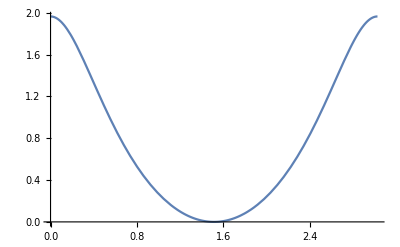

```mathematica
Plot[Evaluate[y[x]/. WaveProfile],{x,0,Period}]
```

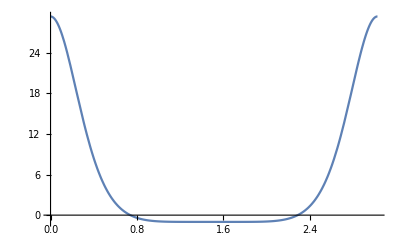

```mathematica
Plot[Pot[x],{x,0,Period}]
```

The code snippet below solves the ODE defining the linearized operator as well as the derivative of this ODE with respect to the eigenvalue parameter λ. This will allow us to generate the monodromy matrix as well as the derivative of the monodromy matrix with respect to the eigenvalue parameter λ. The derivatives are necessary for computing the bifurcation index.

```mathematica
SolMonodromy[l_] := NDSolve[{r1'''[x] + (Pot[x]) r1'[x] - l r1[x]==0,dr1'''[x] + (Pot[x]) dr1'[x] - l dr1[x]-r1[x]==0,r2'''[x] + (Pot[x] ) r2'[x] - l r2[x]==0,dr2'''[x] + (Pot[x] ) dr2'[x] - l dr2[x]- r2[x]==0,r3'''[x] + (Pot[x]) r3'[x] - l r3[x]==0 ,dr3'''[x] + (Pot[x]) dr3'[x] - l dr3[x]-r3[x]==0 ,r1[0]==1,r1'[0]==0,r1''[0]==0,r2[0]==0,r2'[0]==1,r2''[0]==0,r3[0]==0,r3'[0]==0,r3''[0]==1,dr1[0]==0,dr1'[0]==0,dr1''[0]==0,dr2[0]==0,dr2'[0]==0,dr2''[0]==0,dr3[0]==0,dr3'[0]==0,dr3''[0]==0},{r1,r2,r3,dr1,dr2,dr3},{x,0,Period}];
mono[l_] := Evaluate[{{r1[Period],r2[Period],r3[Period]},{r1'[Period],r2'[Period],r3'[Period]},{r1''[Period],r2''[Period],r3''[Period]}}] /. SolMonodromy[l][[1]]
```

The monodromy matrix at λ=0 should have μ=1 as an eigenvalue of geometric multiplicity 2 and algebraic multiplicity 3. The relative error is about .8%.

```mathematica
MatrixForm[mono[0]]
```

(1. | -18.1382 | 1.34993×10^-7
0. | 0.999999 | -2.11387×10^-8
0. | 68.3131 | 0.999999)

```mathematica
Eigenvalues[%]
```

{1.+0. ⅈ,0.999999+0.00120169 ⅈ,0.999999-0.00120169 ⅈ}

The code snippets below compute the characteristic polynomial of the monodromy matrix (CharPoly[λ]), the complex Floquet discriminant (FloqD), the derivative with respect to λ of the  Floquet discriminant (FloqDp), the discriminant of the characteristic polynomial (Disco) and the bifurcation index (BifIndex)

```mathematica
CharPoly[l_] := CharacteristicPolynomial[mono[l] , μ ];
MonoRoots[l_] := μ /. Solve[CharPoly[l]==0,μ];
FloqD[l_] := (Evaluate[r1[Period] + r2'[Period] + r3''[Period]]/. SolMonodromy[l])[[1]]
FloqDp[l_] := (Evaluate[dr1[Period] + dr2'[Period] + dr3''[Period]]/. SolMonodromy[l])[[1]]
Disco[λ_] := Evaluate[(-27-4 Conjugate[r1[Period]+r2'[Period]+r3''[Period]]^3+18 Conjugate[r1[Period]+r2'[Period]+r3''[Period]] (r1[Period]+r2'[Period]+r3''[Period])+Conjugate[r1[Period]+r2'[Period]+r3''[Period]]^2 (r1[Period]+r2'[Period]+r3''[Period])^2-4 (r1[Period]+r2'[Period]+r3''[Period])^3)]/. SolMonodromy[λ][[1]]
BifIndex[l_] := Module[{FF = FloqD[l],FP=FloqDp[l],FPC = Conjugate[FP]},FP^3 + Conjugate[FP]^3 + FF FP Conjugate[FP]^2 + Conjugate[FF] Conjugate[FP] FP^2 ]
```

The plot below depicts the bifurcation index along the imaginary axis (by symmetry this is a real quantity for λ purely imaginary. The plot is turned 90° so that we can see where the plot crosses the y-axis. Those crossings mark bifurcation points.

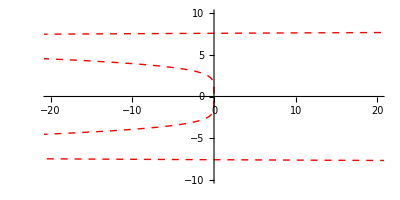

```mathematica
BifIndexPlot=ParametricPlot[{BifIndex[I l],l},{l,-10,10},PlotRange->{{-20,20},{-10,10}},PlotStyle->{Red,Thick,Dashed}]
```

```mathematica
MultiplicityGraph=ParametricPlot[{{0.00002(1-Sign[Discrim[l I]])/2+ I (1+Sign[Discrim[I l]]),l},{-0.00002(1-Sign[Discrim[l I]])/2+ I (1+Sign[Discrim[I l]]),l}},{l,-0.4,0.4},PlotStyle->{{Thick,Magenta},{Thick,Magenta}},PlotRange->{-1,1},PlotPoints->100]
```

-Graphics-

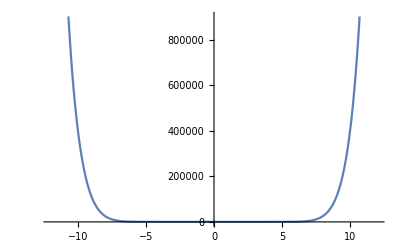

```mathematica
Plot[Discrim[I λ],{λ,-12,12}]
```

```mathematica
(* Deltoid = Locus of points where the (complex) Floquet discriminant has three eigenvalues on the unit circle along the imaginary axis *)
```

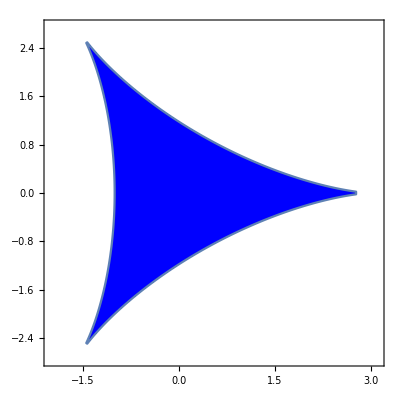

```mathematica
Deltoid1=RegionPlot[-27+18 a^2-8 a^3+a^4+18 b^2+24 a b^2+2 a^2 b^2+b^4<0,{a,-3,3.5},{b,-3.25,3.25},PlotPoints->100,PlotRange->{{-2,3.1},{-2.75,2.75}},PlotStyle->Blue]
```

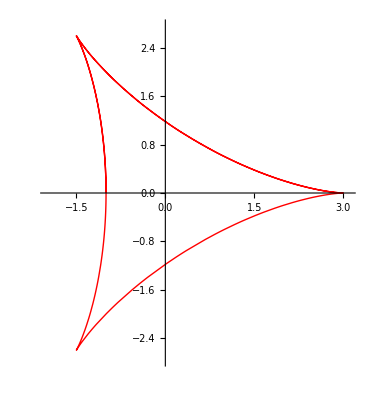

```mathematica
(* This is the Cartesian *)
Astroid[a_,b_,r_] := ParametricPlot[ -r{(a-b) Cos[t] + b Cos[(a-b)/b t],(a-b) Sin[t] + b Sin[(a-b)/b t]},{t,0,6Pi},PlotStyle->{Thick,Red},PlotRange->{{-2,3.1},{-2.75,2.75}}]  
Deltoid2=Astroid[1,2,1]
```

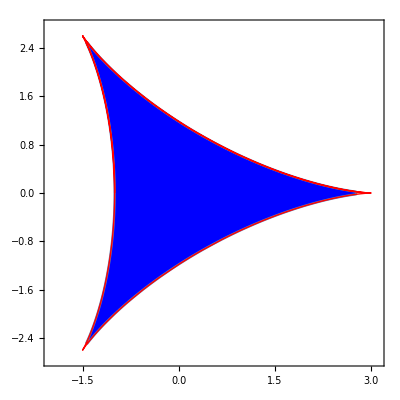

```mathematica
Deltoid3=Show[Deltoid1,Deltoid2]
```

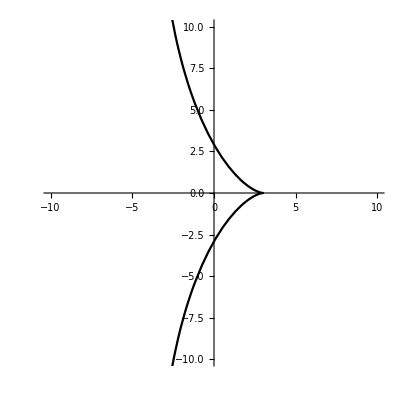

```mathematica
FDPlot=ParametricPlot[{Re[FloqD[I λ]],Im[FloqD[I λ]]},{λ,-10,10},PlotRange->{{-10,10},{-10,10}},PlotStyle->Black]
```

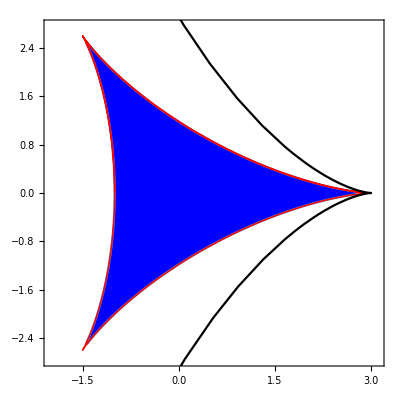

```mathematica
Delt2=Show[Deltoid3,FDPlot]
```

```mathematica
L = Period;
NM = 25;
dx = L/NM;diag = Table[2*Pi*I*1.0(NM-j)/Period,{j,1,2*NM+1}];D1=DiagonalMatrix[diag];
FM = Table[NIntegrate[Exp[2 Pi I k x/Period] Pot[x]/Period,{x,0,Period},AccuracyGoal->15],{k,-2*NM,2*NM}];
FCol = Table[FM[[2NM+2-i]],{i,1,2*NM+1}];
FRow = Table[FM[[i]],{i,2*NM+1,4*NM+1}];
Pot2[x_] := Re[Sum[FM[[k]] Exp[2 Pi I (k-(2*NM+1)) x/Period],{k,1,4*NM+1}]];
PotM = ToeplitzMatrix[Re[FCol],Re[FRow]];
D3=D1.D1.D1;D2=D1.D1;D0=IdentityMatrix[2NM+1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.9475211267033153952545830808394304206269790919608952961539216631}. NIntegrate obtained -7.53608×10^-14+1.81166×10^-14 ⅈ and 9.65165×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.9525394908881486564020747490412839958769271580391047038460783369}. NIntegrate obtained -9.12653×10^-14+1.02388×10^-14 ⅈ and 1.01773×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.8985805958043583029041771450603995010467952252175560801106257713}. NIntegrate obtained -9.13666×10^-14+3.51077×10^-15 ⅈ and 1.12481×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.47311×10^-14-9.3224×10^-15 ⅈ and 7.9727×10^-15 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.01218×10^-13-5.0307×10^-16 ⅈ and 8.24157×10^-15 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.07844×10^-14+9.69884×10^-15 ⅈ and 5.81125×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

Eig[q] and Eig2[q] compute the spectrum with quasi-periodic boundary conditions v(L) = exp(2 π i q/L) v(0). Eig computes the spectrum of the linearized operator and Eig2 computes the spectrum of the adjoint. These should be isospectral. At q=0 both show have a triple eigenvalue of 0. In both cases the zero eigenvalues of of order 2 x10^-5

```mathematica
Eig[q_] := Eigenvalues[D3 - 3I q D2 -3q^2 D1 + I q^3 D0 +  PotM.(D1 - I q D0)];
```

```mathematica
Chop[Eig[0.0]]
```

{1.45519×10^-10+157121. ⅈ,-3.09228×10^-10+139654. ⅈ,-1.30967×10^-10-123540. ⅈ,0.+123534. ⅈ,1.60302×10^-10-108706. ⅈ,0.+108705. ⅈ,0.-95111.8 ⅈ,0.+95111.6 ⅈ,0.-82700.7 ⅈ,-2.05709×10^-10+82700.6 ⅈ,0.-71418.2 ⅈ,0.+71418.2 ⅈ,0.-61210.6 ⅈ,0.+61210.6 ⅈ,0.-52024. ⅈ,0.+52024. ⅈ,0.-43804.7 ⅈ,0.+43804.7 ⅈ,0.-36498.9 ⅈ,0.+36498.9 ⅈ,0.-30053. ⅈ,0.+30053. ⅈ,0.-24413.1 ⅈ,0.+24413.1 ⅈ,0.-19525.6 ⅈ,0.+19525.6 ⅈ,0.-15336.7 ⅈ,0.+15336.7 ⅈ,0.-11792.7 ⅈ,0.+11792.7 ⅈ,0.+8839.76 ⅈ,0.-8839.76 ⅈ,0.-6424.23 ⅈ,0.+6424.23 ⅈ,0.-4492.35 ⅈ,0.+4492.35 ⅈ,0.-2990.38 ⅈ,0.+2990.38 ⅈ,0.+1864.58 ⅈ,0.-1864.58 ⅈ,0.-1061.21 ⅈ,0.+1061.21 ⅈ,0.-526.525 ⅈ,0.+526.525 ⅈ,0.+206.782 ⅈ,0.-206.782 ⅈ,0.-48.1353 ⅈ,0.+48.1353 ⅈ,-2.27966×10^-9+0.0000588901 ⅈ,2.27956×10^-9-0.0000588901 ⅈ,0}

```mathematica
frame=Plot[0,{x,-3.5,3.5},PlotRange->{-10,10}];
l = {}
Do[l=Join[l,Eig[Q]],{Q,-Pi/Period,Pi/Period,.0001}]
Dimensions[l]
```

Find the largest real part to set the scale appropriately.

```mathematica
Max[Re[l]]
```

2.71557

```mathematica
MKdVHotDog= Show[frame,ComplexListPlot[l,PlotStyle->{Blue,PointSize[Small]}],BifIndexPlot]
```

-Graphics-